# The Snowglobe

## 11.

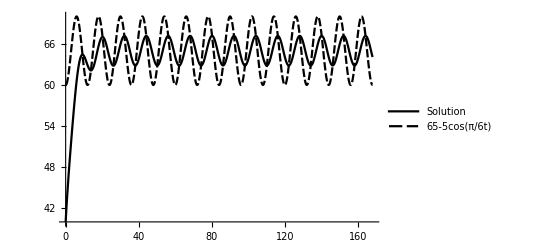

```mathematica
Module[{k,y0,equations,soln},
k=.25;
y0=40;

equations={y'[t]==k(65-5Cos[π/6 t]-y[t]),y[0]==y0};
soln=DSolve[equations,y,t];

Plot[{y[t]/.soln,65-5Cos[π/6 t]},{t,0,24*7},PlotRange->All,PlotLegends->{"Solution","65-5cos(π/6t)"},PlotTheme->"Monochrome"]]
```

The solution to the differential equation appears to mimic the room temperature equation with a slight delay and and a smaller magnitude of oscillation.

## 12.

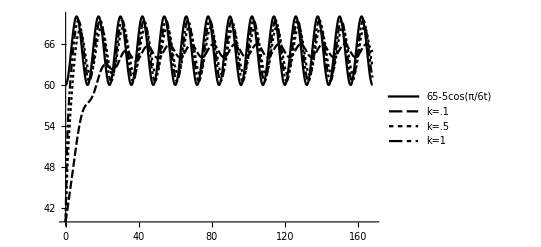

```mathematica
Module[{y0,equations,soln},
y0=40;

equations[k_]={y'[t]==k(65-5Cos[π/6 t]-y[t]),y[0]==y0};
soln[k_]=DSolve[equations[k],y,t];

Plot[Evaluate[Flatten[{65-5Cos[π/6 t],Evaluate[(y[t]/.soln[#])&/@{.1,.5,1}]}]],
{t,0,24*7},
PlotRange->All,PlotTheme->"Monochrome",PlotLegends->{"65-5cos(π/6t)","k=.1","k=.5","k=1"}]]
```

It appears that as k increases, the solution to the differential equation approaches the room temperature faster and also holds closer to the room temperature throughout the day.